```mathematica
wake=1
```

1

```mathematica
RawVals=Import["/Users/brandon/Documents/filecabinet/employment/aquaterra/active.projects/SERDP/Roads/WEPP/wepp.run/cli.met/1-RawTs.csv"];
```

```mathematica
RawValsPre=Import["/Users/brandon/Documents/filecabinet/employment/aquaterra/active.projects/SERDP/Roads/WEPP/wepp.run/cli.met/1-PreInterpolatorRawTs.csv"];
```

```mathematica
absval1={AbsoluteTime[#[[1;;4]]],#[[5]]}&;
RawVals=Map[absval1,RawVals];
```

```mathematica
absval2={AbsoluteTime[#[[1;;4]]],#[[7]]}&;
RawValsPre=Map[absval2,RawValsPre];
```

```mathematica
RawValsInter={};
Print["end="<>ToString[Length[RawValsPre]]]
Monitor[Do[
{
currentval=RawValsPre[[i]];
If[RawVals[[1,1]]≤currentval[[1]]≤RawVals[[-1,1]],RawValsInter=Append[RawValsInter,currentval]];
},{i,1,Length[RawValsPre]}],i]
Clear[RawValsPre];
```

end=513552

```mathematica
Delta=Table[RawValsInter[[i,2]]-RawVals[[i,2]],{i,1,Length[RawValsInter]}];
```

```mathematica
DeltaShowAll=Table[{i,RawVals[[i]],RawValsInter[[i]],Delta[[i]]},{i,1,Length[RawVals]}];
```

```mathematica
DeltaShowSorted=SortBy[DeltaShowAll,#[[4]]&];
```

```mathematica
Column[{Row[{"Minimum Difference:"<>ToString[Min[Delta]]}],Row[{"Maximum Difference:"<>ToString[Max[Delta]]}]}]
```

Minimum Difference:0
Maximum Difference:0.

## Make Day Summary (cumulative of each row per day)

```mathematica
DailySummary={};
Tal=0;
Do[
{
currentval=RawVals[[i]];
Tal+=currentval[[5]];
If[currentval[[4]]==23,{DailySummary=Append[DailySummary,{currentval[[1;;3]],Tal}],Tal=0}];
},{i,1,Length[RawVals]}];
```

## Make Day Summary (min or max of each row per day)

```mathematica
DailySummary={};
DaySet={};
Do[
{
currentval=RawVals[[i]];
DaySet=Append[DaySet,currentval[[5]]];
If[currentval[[4]]==23,{DailySummary=Append[DailySummary,{currentval[[1;;3]],Min[DaySet]}],DaySet={}}];
},{i,1,Length[RawVals]}];
```

## Average Daily per month

```mathematica
MonthBins=Table[{},{i,1,12}];
Tal=0;
DayCount=0;
Do[
{
currentrow=DailySummary[[i]];
DayCount+=1;
Tal+=currentrow[[2]];
currentMonth=currentrow[[1,2]];
If[If[i==Length[DailySummary],True,DailySummary[[i+1,1,2]]≠currentMonth],{MonthBins[[currentMonth]]=Append[MonthBins[[currentMonth]],Tal/DayCount],Tal=0,DayCount=0}];
},{i,1,Length[DailySummary]}];
```

## Average Daily cumulative precip

```mathematica
MonthBins=Table[{},{i,1,12}];
Tal=0;
Do[
{
currentrow=DailySummary[[i]];
Tal+=currentrow[[2]];
currentMonth=currentrow[[1,2]];
If[If[i==Length[DailySummary],True,DailySummary[[i+1,1,2]]≠currentMonth],{MonthBins[[currentMonth]]=Append[MonthBins[[currentMonth]],Tal],Tal=0}];
},{i,1,Length[DailySummary]}];
```

## Plot results

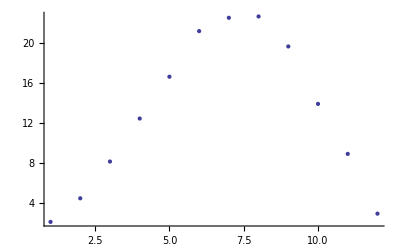
(2.12012
4.47859
8.15197
12.4498
16.6269
21.1847
22.5151
22.6487
19.6527
13.9111
8.91635
2.94466)-Graphics-

```mathematica
MPRECResults=Table[Mean[MonthBins[[i]]],{i,1,Length[MonthBins]}];
Row[{MPRECResults//MatrixForm,ListPlot[MPRECResults]}]
```